# Test Data Preprocessing

These tests require the standard test file resources folder to be downloaded from Git and available at Tests/_resources.

```mathematica
<<NounouW`
```

HokahokaW`
Wed 19 Oct 2016 00:12:59     [Mathematica: 11.0.1 for Microsoft Windows (64-bit) (September 20, 2016)]
     Artifact info as of: Sun 14 Aug 2016 00:05:06
     Local repo path:   C:\prog\_w\HokahokaW\.git
     Current branch [hash]:  dev [e54e12e7076ab93c52f9fd04b9ad2cd5bd18b862]
     Remote:  origin (https://ktakagaki@github.com/ktakagaki/HokahokaW.git)

<<Set JLink` java stack size to 6144Mb>>

NounouW`
Wed 19 Oct 2016 00:13:00     [Mathematica: 11.0.1 for Microsoft Windows (64-bit) (September 20, 2016)]
     Artifact info as of: Thu 4 Aug 2016 11:01:21
     Local repo path:   C:\prog\_w\NounouW\.git
     Current branch [hash]:  dev [c6fa48445eaa327d13d379f0ef7b3853f71ee9ea]
     Remote:  origin (https://github.com/ktakagaki/NounouW.git)

Welcome to nounou, a Scala/Java adapter for neurophysiological data.
Last GIT info from file resource: NNGit.gson.txt
  + current HEAD is: 1a58c41332bd336e036338dfedc8b6c19c080f3e
  + current branch is: master
  + remote names are: https://github.com/ktakagaki/nounou.git, https://github.com/slentzen/nounou.git, https://github.com/dowa4213/nounou.git

```mathematica
Get[ FileNameJoin[{Nest[ParentDirectory,SetDirectory[NotebookDirectory[]],1],"TestDataLoaders.m"}] ];
$nnwResourcesFolder
```

C:\prog\_w\NounouW\resources

```mathematica
(*ShowJavaConsole[]*)
```

## SPP067a

```mathematica
NNWTestLoadSPP067a
```

$nnwTestFileFolder = C:\prog\_w\NounouW\resources\nounou\Neuralynx\SPP067\a

$nnwTestFiles = C:\prog\_w\NounouW\resources\nounou\Neuralynx\SPP067\a\CSC5.ncsC:\prog\_w\NounouW\resources\nounou\Neuralynx\SPP067\a\CSC6.ncsC:\prog\_w\NounouW\resources\nounou\Neuralynx\SPP067\a\CSC7.ncsC:\prog\_w\NounouW\resources\nounou\Neuralynx\SPP067\a\CSC8.ncs

```mathematica
$nnwTestDataOri
```

«JavaObject[nounou.elements.data.NNDataChannelArray]»

```mathematica
$nnwTestDataOri@channelCount[]
```

4

### Timing information

```mathematica
NNPrintInfo[$nnwTestDataOri]
```

nounou.elements.data.NNDataChannelArray(1 segments, fs=32000.0,  , 1a58c41332)
NNTiming(fs=32000.0, segmentCount=1)

NNDataChannelArray(1 segments, fs=32000.0,

```mathematica
NNPrintInfo[$nnwTestDataOri, "Timing"](*testNCS1@getTiming[]@toStringFull[]*)
```

nounou.elements.traits.NNTiming(fs=32000.0, segmentCount=1, 1a58c41332)
==================================================
segment	samples (  mm:ss  ) (    s   )	   start Ts  (  hh:mm )
   0	    607232 (  0:18.98) (    19.0)	  3863862413 ( 0:00.00)

### NNTracePlot

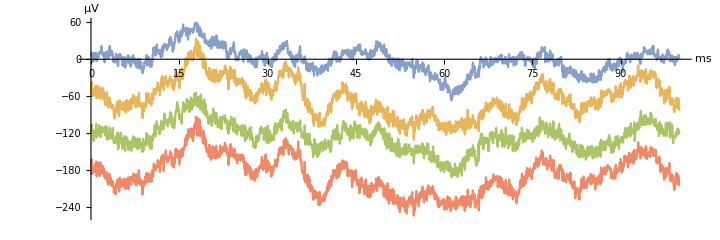

```mathematica
NNTracePlot[$nnwTestDataOri, All, {0 ;; 3200, 0}, NNOptAmplificationFactor-> 16]
```

```mathematica
NNTracePlotManipulate[$nnwTestDataOri, All, Automatic,
 NNOptAmplificationFactor-> 16]
```

!!!Always delete manipulate interface before proceeding!!!

```mathematica
$nnwTestDataMedianSubtract=NNFilterMedianSubtract[$nnwTestDataOri, 81]
```

### NNFilterMedianSubtract

```mathematica
testNCS1Median=NNFilterMedianSubtract[testNCS1, 81]
```

«JavaObject[nounou.elements.data.NNDataChannelExtracted]»

```mathematica
testDataMedianSubtract=NNReadTrace[testNCS1Median,{ 32001;;48000,0}, NNOptReturnTimepoints->False ];
```

```mathematica
LoadJavaClass["nounou.analysis.spikes.SpikeDetect", StaticsVisible->False, AllowShortContext->True]
```

JavaClass[nounou.analysis.spikes.SpikeDetect,<>]

```mathematica
tempSpikes=SpikeDetect`medianSDThresholdPeakDetect[testDataMedianSubtract, 3, 32]
```

{297,331,377,494,689,879,970,1137,1383,1784,1869,2239,2346,2492,2866,2943,3174,3360,3788,3827,3984,4302,4402,4756,5081,5215,5392,5543,6056,6056,6489,6551,6845,6845,7346,7462,7601,8124,8124,8216,8356,8615,8650,9064,9099,9172,9598,9965,10000,10084,10257,10549,11049,11053,11278,11546,11794,12041,12313,12318,12524,12624,12820,12990,13473,13938,14097,14355,14355,14373,14390,14455,14455,14851,14976,15055,15333,15433,15625,15625,15857,15861,15932}

```mathematica
ListLinePlot[testDataMedianSubtract, AspectRatio-> 1/50, ImageSize->100*72,PlotRange->All,
GridLines-> {tempSpikes,None}]//Rasterize
```

-Graphics-

```mathematica
tempTimestamps=SpikeDetect`medianSDThresholdPeakDetect[
testNCS1Median,NN`NNRange[0,320000,1, 0], 3, 32]
```

{10241722731,10238741825,10247169981,10243884325,10244325950,10246297106,10245831544,10237966419,10244681794,10245543950,10243701325,10244495950,10240659731,10246968606,10245799700,10242140950,10238033512,10243979731,10239115794,10243362950,10240776044,10239662419,10244162419,10245068075,10243751325,10245479012,10244530794,10245642981,10247354512,10243960231,10241180856,10246596512,10237881512,10246291481,10239209106,10244619294,10238718669,10246495544,10243508856,10242330637,10239992544,10245923606,10241064044,10245759981,10238982419,10242539075,10246063419,10239743106,10241348950,10244178762,10245287825,10240112981,10242240325,10245433481,10239329356,10237474794,10239054825,10238289106,10238359512,10241781731,10243015325,10246912794,10244523919,10243100512,10237716012,10243341887,10242835762,10245647762,10246450794,10247328637,10242941325,10242699825,10247049856,10238334481,10243784919,10238821856,10245080794,10241371606,10246323012,10240203012,10238303106,10246764919,10241633794,10239425106,10239409325,10241040450,10237479794,10241686762,10237600512,10244566669,10239460575,10239344106,10246924887,10241992012,10241734106,10241490512,10239487200,10239674731,10244244981,10241046356,10239018262,10245347981,10237917294,10239933012,10238957606,10238277731,10239349325,10245672700,10238779200,10238577981,10239239575,10240174606,10244955825,10245328856,10238813794,10242752575,10238465231,10244806575,10237386512,10246616606,10240661950,10238963294,10241318606,10241645169,10242017481,10242639481,10240874294,10244248669,10239355512,10239868387,10239159919,10246795356,10245040606,10246248481,10244213825,10238462825,10243848856,10237828919,10238388700,10240408325,10238056325,10242217731,10242249169,10240996294,10245893044,10242955575,10240465419,10246761887,10245065450,10245942794,10244229512,10238868794,10242352544,10240685481,10241697325,10238258106,10240191044,10243741325,10238536231,10241925731,10239056231,10247247262,10241459887,10240081387,10244504419,10238382544,10238385044,10243822794,10242897481,10247178731,10238080700,10243041169,10244244044,10247152669,10243081544,10239829231,10241379419,10245312481,10242471919,10239813669,10243017981,10237453450,10241703231,10239756544,10246262325,10238659887,10247226981,10243325450,10244387731,10242679856,10240591762,10240627481,10242531262,10247248825,10237505950,10243226731,10241935825,10240602325,10241028075,10246609200,10245591887,10246750450,10240679169,10247263950,10246480075,10245009950,10240188200,10244459981,10240400512,10243065419,10243684731,10243343981,10243580481,10243000044,10237521419,10240779919,10243402169,10237627887,10241980575,10240129169,10242157856,10244650700,10245904044,10238976075,10239596169,10245671262,10245655200,10242121887,10240633137,10244555012,10238193075,10240061981,10241091200,10245596825,10242163887,10239046919,10244851575,10244835419,10242038294,10237596169,10242036856,10242488294,10238127231,10240696731,10238657606,10240428262,10240808294,10240222825,10247232044,10240468981,10242094575,10238079200,10243522231,10237944106,10238881919,10244400950,10240483794,10241077856,10244571669,10240863450,10241213887,10243724950,10239421419,10246438794,10240561325,10246909637,10237703856,10239655762,10245686137,10242874169,10242032481,10238915512,10244932200,10237596575,10242159262,10237427106,10237565825,10245208544,10237576919,10245997575,10246552012,10246972731,10243184794,10243559856,10244476106,10239976762,10237928575,10239194169,10240277387,10239269950,10245606950,10240078044,10245149606,10238917012,10237621637,10243851231,10240923044,10245666606,10240310262,10240567481,10244743669,10242627981,10242346419,10244667325,10239293762,10247361575,10239053106,10242016794,10239753606,10241729075,10242576544,10238546481,10241557200,10239529294,10243549887,10242393262,10242220200,10245051481,10238702919,10245517356,10242686669,10243609137,10245817137,10243229731,10243406262,10243571137,10244769106,10244536387,10241504075,10237485044,10242137919,10244993794,10244058669,10238934731,10239724762,10239405262,10244983231,10239805794,10243439825,10244974762,10243954637,10242424700,10247080606,10239545106,10243786137,10244119450,10246848575,10241309200,10237884950,10246802856,10238369887,10243483919,10242415887,10238822419,10240234075,10238238325,10238161231,10242333669,10239178044,10245909169,10241880575,10238003762,10240019919,10240912044,10237450981,10239658637,10239113231,10241345606,10237772387,10243295544,10238322825,10244392919,10238478262,10244801200,10246898419,10237460294,10244198637,10242838262,10239095544,10242799231,10238944856,10243522387,10244060294,10240545356,10238169481,10246865512,10240326106,10240670450,10242431919,10240934762,10239183887,10242638012,10242285981,10246882700,10237516294,10243109419,10243933512,10241401919,10242864950,10246024856,10242804637,10244471637,10242048231,10246841481,10245677231,10239730856,10237850387,10246498419,10240565762,10245531606,10241944450,10238688387,10238110606,10243677200,10240635356,10244046669,10242056481,10243659950,10238128856,10238091075,10238121044,10242676856,10241194512,10237692169,10244498637,10246493075,10239131481,10247228825,10245131325,10246278825,10240564387,10240857887,10245561919,10245870137,10242663887,10246725075,10237483981,10241686294,10246275731,10242832262,10246131544,10247013450,10245180919,10238292481,10237679637,10241571762,10237823856,10237580606,10238562512,10237612012,10240377512,10244964387,10242302481,10243145325,10240050387,10246017325,10238841262,10239277075,10242223387,10245912794,10237374262,10245281481,10247264294,10240872575,10242969950,10242311075,10242652731,10238242200,10240933231,10247079544,10246921450,10241544887,10240449200,10237961262,10244519762,10245512919,10240573481,10237836387,10243615044,10243644137,10241971481,10239339012,10237514950,10240352262,10246536794,10242497262,10241508544,10238049919,10245875731,10240621512,10237808200,10239974169,10242382762,10245702981,10243924200,10246246794,10246149044,10245871887,10244440919,10244514637,10244569731,10237552887,10242980856,10242079231,10239084450,10247205044,10238758200,10237883950,10246896794,10245805825,10241820669,10238273231,10242714075,10239465294,10244488044,10247345606,10240786481,10241303137,10242155262,10240764856,10242951700,10247140981,10243258544,10238992419,10239691731,10241036044,10245855262,10242580887,10242624700,10245377169,10246164887,10242921637,10245862669,10245444919,10237536294,10246831137,10243417637,10242519075,10246097669,10241365856,10242185794,10243489950,10239532481,10237852450,10244195075,10243164794,10239639919,10243834544,10242278012,10244006575,10239512200,10239623825,10244151794,10237394325,10245344606,10238472450,10240545887,10245084075,10238178700,10241009356,10245235762,10243060825,10239272887,10244023387,10240438450,10243330012,10240346762,10241517419,10240885169,10239245606,10246931044,10241745012,10245134231,10238338044,10240579981,10246000294,10247310981,10242373794,10243049669,10246668950,10238861544,10246152919,10242323419,10239853794,10240030231,10246550825,10240715856,10238767762,10242561981,10246520575,10244277606,10246779794,10243629669,10237620512,10239255044,10246938231,10243432669,10242126575,10246364794,10238015231,10237974919,10239447856,10242564450,10242894356,10244031856,10247280544,10247109919,10244167169,10239305262,10239117544,10245261262,10241026887,10242985450,10245072856,10243045606,10242767637,10243803325,10241851137,10245724106,10242594450,10238229137,10240827356,10239147606,10246734075,10245737075,10239740856,10244305669,10245328325,10246465762,10242448544,10237435262,10242727825,10240629700,10237802919,10239267919,10244875700,10242908919,10238223731,10243506012,10241469419,10237660512,10240247762,10247054137,10245920950,10241198575,10237424450,10246577512,10244129294,10243648887,10245493919,10243939700,10238321294,10245980637,10244635325,10238353762,10247271575,10247278762,10241427700,10238868919,10241389325,10238492856,10241477669,10241759887,10246301356,10241555762,10245223450,10240498575,10246287825,10240238231,10240263356,10245778887,10245522950,10239856919,10241271981,10239686919,10246176856,10246311106,10245253044,10238175887,10237490262,10243210356,10243771356,10238256825,10237730012,10242170794,10242335450,10241782387,10240128200,10243108262,10241241512,10243509919,10245164825,10244593169,10238931231,10245439669,10238794294,10246302887,10243715481,10239959106,10244318637,10242610075,10244047981,10245280387,10245708450,10239223637,10243372450,10241896950,10237896919,10246488887,10240801700,10237834200,10243518919,10243599450,10238507700,10243076450,10241652450,10239990200,10237718012,10246640356,10237459012,10238693794,10240423169,10242203919,10239880700,10239928262,10243634794,10239896106,10244081200,10247034169,10244619887,10241960106,10243157544,10246950512,10237788262,10246671887,10241309356,10244539481,10245073419,10245562794,10243616887,10246456981,10243537825,10245877887,10238837356,10246820012,10241146700,10245692294,10246545450,10243663544,10242214512,10238899044,10246401137,10244303606,10238998262,10244089981,10240239887,10242232200,10242935575,10239353919,10238327700,10245748200,10244560731,10237691544,10239212481,10241718262,10245731294,10239280325,10240109981,10239386106,10243353606,10239762325,10240428169,10245974106,10247371606,10241127544,10242501606,10243767356,10243113012,10244977887,10244210981,10244120919,10242376887,10244915700,10246673356,10243092137,10244042075,10242801950,10241492419,10245578544,10238118950,10243232856,10242264262,10237629012,10241203825,10246688606,10239261231,10238642481,10241166794,10246327012,10245598856,10239627825,10245544762,10243894012,10243275419,10244984044,10240919231,10244345200,10239837481,10246914262,10243131044,10243279669,10242671450,10241264294,10237676200,10238824981,10243441075,10245025981,10246033294,10239614387,10243863512,10239341075,10246426700,10246593419,10237419262,10244547544,10243478762,10241663387,10237503262,10242533887,10239253544,10238211950,10244514762,10245547137,10245838825,10242319106,10246733044,10247095950,10238852419,10240248512,10242001325,10243971512,10242541231,10245593575,10246079450,10243516700,10241015544,10244237294,10245936669,10244273106,10242878981,10238673200,10241162231,10239791669,10242342012,10242440856,10244201200,10240196387,10240856481,10244850762,10238758044,10244784012,10245658294,10238606450,10242939481,10240453981,10245184075,10240267856,10243448419,10242618387,10237434262,10243950325,10238521887,10242480950,10238222419,10246439606,10241858044,10241790075,10238416481,10246376169,10246685481,10240353794,10246050887,10245103419,10246132856,10245644575,10241104637,10240890544,10238734075,10243832544,10246432637,10246117669,10241106700,10245502575,10238311169,10243481200,10238199919,10243730887,10245175950,10239807200,10245510950,10244362450,10237999200,10241620200,10243756169,10241586950,10241197012,10238429012,10243124731,10242549137,10240330794,10243709544,10238491637,10243200200,10241842856,10245532794,10238901887,10241764169,10246391731,10244333606,10239068637,10238497762,10242547325,10241669481,10241066731,10239560575,10245619856,10238871137,10237911012,10239100419,10244884575,10237639544,10245232700,10240597075,10241237387,10247124231,10241098575,10241636169,10245195544,10244261825,10241951794,10241012544,10244960325,10242400887,10246953856,10240743637,10245519169,10239612419,10245142075,10241864762,10242515356,10243243669,10238064075,10246591825,10243867731,10246262731,10239299544,10238158512,10246284169,10240206419,10243070387,10242848262,10241225544,10237765606,10242784356,10238143575,10237610700,10242236669,10245753325,10237550887,10237963419,10240035419,10246196325,10244873575,10240255856,10245017731,10247195106,10245345200,10239479044,10245784356,10247142294,10246384887,10238627137,10243310481,10244215356,10247341575,10241891481,10238929044,10239944294,10243494262,10243277044,10243524294,10245000231,10242088575,10240903887,10242399637,10242816919,10243602731,10239699450,10246652700,10245056700,10241395544,10239864700,10239917075,10239285794,10247162262,10237886325,10244837262,10246585575,10246341481,10240906481,10239578419,10242529106,10245455544,10239821387,10242351606,10237986450,10245091169,10240367544,10244737137,10239500075,10240251575,10242367106,10243572825,10243801544,10239313919,10244753137,10245420450,10247087669,10244669169,10242164419,10241798856,10238341075,10241681137,10242903356,10246856544,10240244544,10243394137,10245646294,10245676419,10240958981,10242578856,10246374387,10237376981,10241540669,10240393262,10238843731,10241452856,10239162700,10242772825,10243575200,10244288169,10241178544,10244778200,10241629294,10246749450,10245954637,10246625637,10243290419,10244074169,10238107544,10241147700,10244974012,10240530200,10243463794,10243171731,10244113825,10247332106,10246369169,10237735231,10242738700,10246037106,10237753200,10240065825,10241766825,10247154981,10241538012,10243554512,10241031231,10238773887,10245497981,10239256044,10239358544,10244228044,10240950637,10240988575,10238855544,10243562012,10239912262,10239514169,10243633387,10243678794,10247030137,10244343544,10246354169,10244628825,10237612700,10243345075,10238239075,10245360606,10245985325,10241051825,10245298075,10247201575,10242725044,10240141419,10246101012,10247112606,10244648137,10240005012,10245118794,10246238575,10239576981,10242821200,10242854512,10241665387,10243113137,10238254856,10242476294,10243751919,10246114794,10242455762,10241362231,10246561481,10242599356,10246703575,10246971075,10240403012,10246602731,10246338637,10238305731,10239948794,10240433169,10241410981,10240695231,10240888606,10247366012,10242644075,10238443231,10240970512,10238094231,10238446575,10243456700,10241536669,10243033825,10238019950,10246632887,10238318450,10240148544,10238970075,10242604481,10242499387,10241478731,10245875856,10238148637,10246988512,10237977919,10244029137,10245216419,10240361544,10242269794,10244963231,10242039762,10246215169,10246103356,10241111794,10247305794,10245077106,10243537481,10244899887,10246568887,10239592825,10246641950,10238886544,10238541762,10245558137,10239517137,10242290887,10240336575,10241588262,10240826544,10242655169,10241775294,10244106669,10247019075,10241902512,10238587169,10244636325,10240748794,10241495544,10238431669,10238366075,10238576044,10240869169,10239701981,10239450294,10243351387,10246871075,10245768669,10239694981,10241572637,10239110950,10242269262,10244343669,10243521387,10240296669,10243264044,10239387544,10240646606,10237933981,10243373762,10238408794,10245815669,10242201887,10242497387,10241313294,10241848294,10243618700,10243878169,10244815950,10243034731,10239482856,10241286950,10240987012,10245160544,10244349012,10239498044,10238808825,10247103544,10245424544,10246810606,10247211981,10237676731,10246440887,10244455325,10244917731,10245720700,10246472981,10245409012,10238725700,10243908294,10246180356,10246471262,10245748856,10246011169,10243154637,10240700294,10247291856,10238196919,10243990856,10244728356,10245265481,10245320231,10245296856,10240811075,10246802137,10245888575,10239170700,10238923950,10239036169,10242458669,10241751794,10246640481,10240954075,10246307606,10238403575,10239603512,10241916825,10241804856,10245313169,10241202200,10242701606,10242903981,10246360200,10242661544,10238885169,10245659481,10239777950,10241569356,10243216294,10239671606,10246204481,10243423044,10245488981,10245964231,10238400731,10246081419,10240842106,10240272200,10243324481,10237644575,10240524856,10239535887,10237707231,10245805950,10240900325,10244588137,10243818044,10245829669,10244374325,10238685762,10244411919,10243002231,10247216762,10242357169,10238394794,10240731575,10244703356,10240264325,10243694387,10245741325,10241082825,10239718012,10243014137,10241443825,10243925731,10240227981,10241714075,10243765700,10238383606,10242991294,10244950450,10240879606,10242503544,10247098262,10244820731,10247185762,10242233637,10241476356,10239063075,10243729856,10242372356,10245389856,10237866262,10246146075,10241426262,10242265575,10246243044,10244491950,10246826012,10247355387,10245393325,10240966137,10243586575,10241878044,10241230950,10239981231,10244064075,10238602825,10243893544,10244868294,10245459794,10243983762,10238221325,10244508044,10243247950,10239869419,10238451137,10244210887,10237958981,10243129419,10243204544,10245399794,10242178887,10245789950,10241296794,10239175856,10241602137,10237564700,10237912544,10244136325,10240576200,10245476981,10246781950,10239002387,10240613231,10246701575,10239434544,10243913325,10245345044,10245238575,10240018669,10243994200,10245276450,10237784450,10243734637,10238034887,10242795856,10241445231,10244083481,10240577106,10239898919,10241329325,10243291981,10245611325,10244717450,10241363606,10243164887,10239397887,10238718544,10243691606,10244285200,10238532044,10239446294,10240711669,10244182669,10243670231,10242924137,10240977106,10245847544,10244858887,10244552887,10247347325,10244698200,10246571387,10243178106,10239371512,10244817419,10240094137,10238104825,10244553044,10240125419,10240980794,10244097669,10242537950,10239819481,10245757137,10240304262,10239346481,10246037762,10238982575,10241100044,10237740575,10241507950,10241209950,10239344700,10243651669,10240331981,10244713387,10247350512,10243301544,10238656512,10241464544,10239777294,10244759169,10242709419,10244258887,10240013981,10245487544,10238226731,10238822950,10237413356,10246212762,10246568731,10239608325,10247317794,10243386419,10238966794,10242802825,10239015044,10240547669,10246769794,10238918575,10239816669,10246012325,10244967294,10240143606,10237950044,10237604762,10237925387,10245104419,10242107856,10245655044,10238630012,10240514169,10241439950,10237900575,10240606137,10243120825,10247139512,10245410294,10239900606,10243967075,10243357887,10240288606,10237532856,10241632169,10239615794,10246600669,10242464887,10240158856,10244666044,10240384637,10243417887,10244603419,10246620012,10241779606,10244947419,10244376137,10245200106,10242288950,10244439669,10245087887,10238133419,10241015637,10237988669,10240795700,10241256575,10246657387,10238187137,10238286700,10245637606,10244934575,10243179700,10246910544,10242554794,10242943794,10237443575,10243816856,10239033137,10242073387,10244375606,10239192137,10242063700,10247129325,10245471387,10239716700,10246718669,10244208575,10242887106,10242317919,10247012231,10240173450,10243390169,10244424575,10242870419,10241713231,10244771012,10244407700,10246512762,10242409481,10240038794,10241418450,10240316794,10243667825,10242863637,10239372731,10240870200,10241735262,10243304575,10239746669,10245167012,10246408512,10243133575,10247300700,10244013950,10237818325,10238610794,10241280137,10244737981,10237753981,10245505981,10241835981,10238156575,10238684669,10245969919,10241185012,10244919544,10239726262,10240465512,10244720012,10241649887,10244793731,10246227262,10243030606,10247004169,10242513012,10246980419,10240096669,10245886169,10241129762,10245938887,10242111106,10239126919,10239845044,10246031137,10246814794,10241747262,10246258856,10237974200,10244360137,10243916950,10246798450,10242074887,10238634387,10244900544,10245705481,10238174450,10245289950,10239283950,10241617575,10238749544,10237996606,10242090012,10245592012,10247065262,10241333606,10241115012,10245681419,10241986325,10242741794,10239675575,10243097387,10238764637,10240824950,10238510825,10246048106,10237411825,10245631356,10242262856,10242534637,10245247481,10238643575,10240215731}

```mathematica
ListLinePlot[
NNReadTrace[testNCS1Median,{ 0;;48000,0}, NNOptReturnTimepoints->"Timestamps" ], 
AspectRatio-> 1/50, ImageSize->100*72,PlotRange->All,
GridLines-> {tempTimestamps,None}]//Rasterize
```

-Graphics-

## NCS1 (E04LC: single channel, many segments)

```mathematica
testNCS1 = NNLoad[ FileNameJoin[{resourceDataDirectory,"E04LC","CSC1.ncs"}] ]
```

«JavaObject[nounou.io.neuralynx.NNDataChannelFileReadNCS]»

### Timing information

```mathematica
testNCS1@getTiming[]@toString[]
```

NNTiming(fs=32000.0, segmentCount=94)

```mathematica
NNPrintInfo[testNCS1]
```

nounou.io.neuralynx.NNDataChannelFileReadNCS(94 segments, fs=32000.0, file=C:\prog\_w\NounouW\NounouW\Tests\_resources\nounou\Neuralynx\E04LC\CSC1.ncs, 353bff1ccc)

```mathematica
NNPrintInfo[testNCS1, "Timing"](*testNCS1@getTiming[]@toStringFull[]*)
```

nounou.elements.traits.NNTiming(fs=32000.0, segmentCount=94, 353bff1ccc)
================================================================================
segment	samples (  mm:ss  ) (    s   )	   start Ts  (  hh:mm )
   0	   2546176 (  1:19.57) (    79.6)	 10237373231 ( 0:00.00)
   1	   2170880 (  1:07.84) (    67.8)	 10664245949 ( 0:07.11)
   2	   2305024 (  1:12.03) (    72.0)	 10754519949 ( 0:08.62)
   3	   2161664 (  1:07.55) (    67.6)	 10850791949 ( 0:10.22)
   4	   2997760 (  1:33.68) (    93.7)	 11295016949 ( 0:17.63)
   5	   2387456 (  1:14.61) (    74.6)	 11487035949 ( 0:20.83)
   6	   2265088 (  1:10.78) (    70.8)	 11583690949 ( 0:22.44)
   7	   2387456 (  1:14.61) (    74.6)	 11683015949 ( 0:24.09)
   8	   3902976 (  2:01.97) (   122.0)	 11827212949 ( 0:26.50)
   9	   2618368 (  1:21.82) (    81.8)	 11983644949 ( 0:29.10)
  10	   1647104 (  0:51.47) (    51.5)	 12072501949 ( 0:30.59)
  11	   1575424 (  0:49.23) (    49.2)	 12133226949 ( 0:31.60)
  12	   3245056 (  1:41.41) (   101.4)	 12288899949 ( 0:34.19)
  13	   2422784 (  1:15.71) (    75.7)	 12409025949 ( 0:36.19)
  14	   2198528 (  1:08.70) (    68.7)	 12498510949 ( 0:37.69)
  15	   2352128 (  1:13.50) (    73.5)	 12579165949 ( 0:39.03)
  16	   2157568 (  1:07.42) (    67.4)	 12741120949 ( 0:41.73)
  17	   2134528 (  1:06.70) (    66.7)	 12858471949 ( 0:43.68)
  18	   2119680 (  1:06.24) (    66.2)	 12936582949 ( 0:44.99)
  19	   2090496 (  1:05.33) (    65.3)	 13017219949 ( 0:46.33)
  20	   2553344 (  1:19.79) (    79.8)	 13093847949 ( 0:47.61)
  21	   1839616 (  0:57.49) (    57.5)	 16591906949 ( 1:45.91)
  22	   1851392 (  0:57.86) (    57.9)	 16672396949 ( 1:47.25)
  23	   1785344 (  0:55.79) (    55.8)	 16753077949 ( 1:48.60)
  24	   1777152 (  0:55.54) (    55.5)	 16830067949 ( 1:49.88)
  25	   2441216 (  1:16.29) (    76.3)	 16973049949 ( 1:52.26)
  26	   1899520 (  0:59.36) (    59.4)	 21828656668 ( 3:13.19)
  27	   1888256 (  0:59.01) (    59.0)	 21913111668 ( 3:14.60)
  28	   1721856 (  0:53.81) (    53.8)	 21991294668 ( 3:15.90)
  29	   1846784 (  0:57.71) (    57.7)	 22066383668 ( 3:17.15)
  30	   2132992 (  1:06.66) (    66.7)	 22160885668 ( 3:18.73)
  31	   2460160 (  1:16.88) (    76.9)	 22251740668 ( 3:20.24)
  32	   2265088 (  1:10.78) (    70.8)	 22352220668 ( 3:21.91)
  33	   2185216 (  1:08.29) (    68.3)	 22445369668 ( 3:23.47)
  34	   3800064 (  1:58.75) (   118.8)	 22580372668 ( 3:25.72)
  35	   2446848 (  1:16.46) (    76.5)	 22705665668 ( 3:27.80)
  36	   1822208 (  0:56.94) (    56.9)	 22805852668 ( 3:29.47)
  37	   1444352 (  0:45.14) (    45.1)	 22870117668 ( 3:30.55)
  38	   2193920 (  1:08.56) (    68.6)	 22968880668 ( 3:32.19)
  39	   2121728 (  1:06.30) (    66.3)	 23062295668 ( 3:33.75)
  40	   2095104 (  1:05.47) (    65.5)	 23137806668 ( 3:35.01)
  41	   2156544 (  1:07.39) (    67.4)	 23280545668 ( 3:37.39)
  42	   2127360 (  1:06.48) (    66.5)	 23370969668 ( 3:38.89)
  43	   2094592 (  1:05.46) (    65.5)	 23438459668 ( 3:40.02)
  44	   2126848 (  1:06.46) (    66.5)	 23504924668 ( 3:41.13)
  45	   2122240 (  1:06.32) (    66.3)	 23573259668 ( 3:42.26)
  46	   1861632 (  0:58.18) (    58.2)	 23863260668 ( 3:47.10)
  47	   1770496 (  0:55.33) (    55.3)	 23940016668 ( 3:48.38)
  48	   1795584 (  0:56.11) (    56.1)	 24017169668 ( 3:49.66)
  49	   1971712 (  1:01.62) (    61.6)	 24107428668 ( 3:51.17)
  50	   2276352 (  1:11.14) (    71.1)	 24266401668 ( 3:53.82)
  51	   2361344 (  1:13.79) (    73.8)	 24363958668 ( 3:55.44)
  52	   2138624 (  1:06.83) (    66.8)	 24457817668 ( 3:57.01)
  53	   2222592 (  1:09.46) (    69.5)	 24540061668 ( 3:58.38)
  54	   3304448 (  1:43.26) (   103.3)	 24660859668 ( 4:00.39)
  55	   2171904 (  1:07.87) (    67.9)	 24773137668 ( 4:02.26)
  56	   1558528 (  0:48.70) (    48.7)	 24847062668 ( 4:03.49)
  57	   1312256 (  0:41.01) (    41.0)	 24901896668 ( 4:04.41)
  58	   3031040 (  1:34.72) (    94.7)	 24986582668 ( 4:05.82)
  59	   2152448 (  1:07.26) (    67.3)	 25092887668 ( 4:07.59)
  60	   2109440 (  1:05.92) (    65.9)	 25161342668 ( 4:08.73)
  61	   2138112 (  1:06.82) (    66.8)	 25227915668 ( 4:09.84)
  62	   2124800 (  1:06.40) (    66.4)	 25306722668 ( 4:11.16)
  63	   2082816 (  1:05.09) (    65.1)	 25374353668 ( 4:12.28)
  64	   2061312 (  1:04.42) (    64.4)	 25440635668 ( 4:13.39)
  65	   2149888 (  1:07.18) (    67.2)	 25506333668 ( 4:14.48)
  66	   1409024 (  0:44.03) (    44.0)	 25618652668 ( 4:16.35)
  67	   1364992 (  0:42.66) (    42.7)	 25686017668 ( 4:17.48)
  68	   1436672 (  0:44.90) (    44.9)	 25749983668 ( 4:18.54)
  69	   1519104 (  0:47.47) (    47.5)	 25813277668 ( 4:19.60)
  70	   1218560 (  0:38.08) (    38.1)	 26345810668 ( 4:28.47)
  71	   1157632 (  0:36.18) (    36.2)	 26401762668 ( 4:29.41)
  72	   1254912 (  0:39.22) (    39.2)	 26454941668 ( 4:30.29)
  73	   1192960 (  0:37.28) (    37.3)	 26520655668 ( 4:31.39)
  74	    817152 (  0:25.54) (    25.5)	 26628122668 ( 4:33.18)
  75	    733696 (  0:22.93) (    22.9)	 26676912668 ( 4:33.99)
  76	    558592 (  0:17.46) (    17.5)	 26716099668 ( 4:34.65)
  77	    545280 (  0:17.04) (    17.0)	 26745030668 ( 4:35.13)
  78	    700928 (  0:21.90) (    21.9)	 26784192668 ( 4:35.78)
  79	    702976 (  0:21.97) (    22.0)	 26819926668 ( 4:36.38)
  80	    757248 (  0:23.66) (    23.7)	 26866786668 ( 4:37.16)
  81	    644096 (  0:20.13) (    20.1)	 26903900668 ( 4:37.78)
  82	    769024 (  0:24.03) (    24.0)	 27119439668 ( 4:41.37)
  83	    592896 (  0:18.53) (    18.5)	 27165320668 ( 4:42.13)
  84	   1137664 (  0:35.55) (    35.6)	 27199193668 ( 4:42.70)
  85	    961024 (  0:30.03) (    30.0)	 27247321668 ( 4:43.50)
  86	    455680 (  0:14.24) (    14.2)	 27298549668 ( 4:44.35)
  87	    493568 (  0:15.42) (    15.4)	 27324851668 ( 4:44.79)
  88	    471552 (  0:14.74) (    14.7)	 27354091668 ( 4:45.28)
  89	    418816 (  0:13.09) (    13.1)	 27382801668 ( 4:45.76)
  90	    388608 (  0:12.14) (    12.1)	 27415681668 ( 4:46.31)
  91	    386560 (  0:12.08) (    12.1)	 27440978668 ( 4:46.73)
  92	    370176 (  0:11.57) (    11.6)	 27468093668 ( 4:47.18)
  93	    368640 (  0:11.52) (    11.5)	 27488854668 ( 4:47.52)

### NNReadTrace

```mathematica
testData=NNReadTrace[testNCS1,{ 32001;;48000,0}, NNOptReturnTimepoints->False ];
```

```mathematica
ListLinePlot[testData, AspectRatio-> 1/50, ImageSize->100*72]//Rasterize
```

-Graphics-

### NNFilterMedianSubtract

```mathematica
testNCS1Median=NNFilterMedianSubtract[testNCS1, 81]
```

«JavaObject[nounou.elements.data.NNDataChannelExtracted]»

```mathematica
testDataMedianSubtract=NNReadTrace[testNCS1Median,{ 32001;;48000,0}, NNOptReturnTimepoints->False ];
```

```mathematica
LoadJavaClass["nounou.analysis.spikes.SpikeDetect", StaticsVisible->False, AllowShortContext->True]
```

JavaClass[nounou.analysis.spikes.SpikeDetect,<>]

```mathematica
tempSpikes=SpikeDetect`medianSDThresholdPeakDetect[testDataMedianSubtract, 3, 32]
```

{297,331,377,494,689,879,970,1137,1383,1784,1869,2239,2346,2492,2866,2943,3174,3360,3788,3827,3984,4302,4402,4756,5081,5215,5392,5543,6056,6056,6489,6551,6845,6845,7346,7462,7601,8124,8124,8216,8356,8615,8650,9064,9099,9172,9598,9965,10000,10084,10257,10549,11049,11053,11278,11546,11794,12041,12313,12318,12524,12624,12820,12990,13473,13938,14097,14355,14355,14373,14390,14455,14455,14851,14976,15055,15333,15433,15625,15625,15857,15861,15932}

```mathematica
ListLinePlot[testDataMedianSubtract, AspectRatio-> 1/50, ImageSize->100*72,PlotRange->All,
GridLines-> {tempSpikes,None}]//Rasterize
```

-Graphics-

```mathematica
tempTimestamps=SpikeDetect`medianSDThresholdPeakDetect[
testNCS1Median,NN`NNRange[0,320000,1, 0], 3, 32]
```

{10241722731,10238741825,10247169981,10243884325,10244325950,10246297106,10245831544,10237966419,10244681794,10245543950,10243701325,10244495950,10240659731,10246968606,10245799700,10242140950,10238033512,10243979731,10239115794,10243362950,10240776044,10239662419,10244162419,10245068075,10243751325,10245479012,10244530794,10245642981,10247354512,10243960231,10241180856,10246596512,10237881512,10246291481,10239209106,10244619294,10238718669,10246495544,10243508856,10242330637,10239992544,10245923606,10241064044,10245759981,10238982419,10242539075,10246063419,10239743106,10241348950,10244178762,10245287825,10240112981,10242240325,10245433481,10239329356,10237474794,10239054825,10238289106,10238359512,10241781731,10243015325,10246912794,10244523919,10243100512,10237716012,10243341887,10242835762,10245647762,10246450794,10247328637,10242941325,10242699825,10247049856,10238334481,10243784919,10238821856,10245080794,10241371606,10246323012,10240203012,10238303106,10246764919,10241633794,10239425106,10239409325,10241040450,10237479794,10241686762,10237600512,10244566669,10239460575,10239344106,10246924887,10241992012,10241734106,10241490512,10239487200,10239674731,10244244981,10241046356,10239018262,10245347981,10237917294,10239933012,10238957606,10238277731,10239349325,10245672700,10238779200,10238577981,10239239575,10240174606,10244955825,10245328856,10238813794,10242752575,10238465231,10244806575,10237386512,10246616606,10240661950,10238963294,10241318606,10241645169,10242017481,10242639481,10240874294,10244248669,10239355512,10239868387,10239159919,10246795356,10245040606,10246248481,10244213825,10238462825,10243848856,10237828919,10238388700,10240408325,10238056325,10242217731,10242249169,10240996294,10245893044,10242955575,10240465419,10246761887,10245065450,10245942794,10244229512,10238868794,10242352544,10240685481,10241697325,10238258106,10240191044,10243741325,10238536231,10241925731,10239056231,10247247262,10241459887,10240081387,10244504419,10238382544,10238385044,10243822794,10242897481,10247178731,10238080700,10243041169,10244244044,10247152669,10243081544,10239829231,10241379419,10245312481,10242471919,10239813669,10243017981,10237453450,10241703231,10239756544,10246262325,10238659887,10247226981,10243325450,10244387731,10242679856,10240591762,10240627481,10242531262,10247248825,10237505950,10243226731,10241935825,10240602325,10241028075,10246609200,10245591887,10246750450,10240679169,10247263950,10246480075,10245009950,10240188200,10244459981,10240400512,10243065419,10243684731,10243343981,10243580481,10243000044,10237521419,10240779919,10243402169,10237627887,10241980575,10240129169,10242157856,10244650700,10245904044,10238976075,10239596169,10245671262,10245655200,10242121887,10240633137,10244555012,10238193075,10240061981,10241091200,10245596825,10242163887,10239046919,10244851575,10244835419,10242038294,10237596169,10242036856,10242488294,10238127231,10240696731,10238657606,10240428262,10240808294,10240222825,10247232044,10240468981,10242094575,10238079200,10243522231,10237944106,10238881919,10244400950,10240483794,10241077856,10244571669,10240863450,10241213887,10243724950,10239421419,10246438794,10240561325,10246909637,10237703856,10239655762,10245686137,10242874169,10242032481,10238915512,10244932200,10237596575,10242159262,10237427106,10237565825,10245208544,10237576919,10245997575,10246552012,10246972731,10243184794,10243559856,10244476106,10239976762,10237928575,10239194169,10240277387,10239269950,10245606950,10240078044,10245149606,10238917012,10237621637,10243851231,10240923044,10245666606,10240310262,10240567481,10244743669,10242627981,10242346419,10244667325,10239293762,10247361575,10239053106,10242016794,10239753606,10241729075,10242576544,10238546481,10241557200,10239529294,10243549887,10242393262,10242220200,10245051481,10238702919,10245517356,10242686669,10243609137,10245817137,10243229731,10243406262,10243571137,10244769106,10244536387,10241504075,10237485044,10242137919,10244993794,10244058669,10238934731,10239724762,10239405262,10244983231,10239805794,10243439825,10244974762,10243954637,10242424700,10247080606,10239545106,10243786137,10244119450,10246848575,10241309200,10237884950,10246802856,10238369887,10243483919,10242415887,10238822419,10240234075,10238238325,10238161231,10242333669,10239178044,10245909169,10241880575,10238003762,10240019919,10240912044,10237450981,10239658637,10239113231,10241345606,10237772387,10243295544,10238322825,10244392919,10238478262,10244801200,10246898419,10237460294,10244198637,10242838262,10239095544,10242799231,10238944856,10243522387,10244060294,10240545356,10238169481,10246865512,10240326106,10240670450,10242431919,10240934762,10239183887,10242638012,10242285981,10246882700,10237516294,10243109419,10243933512,10241401919,10242864950,10246024856,10242804637,10244471637,10242048231,10246841481,10245677231,10239730856,10237850387,10246498419,10240565762,10245531606,10241944450,10238688387,10238110606,10243677200,10240635356,10244046669,10242056481,10243659950,10238128856,10238091075,10238121044,10242676856,10241194512,10237692169,10244498637,10246493075,10239131481,10247228825,10245131325,10246278825,10240564387,10240857887,10245561919,10245870137,10242663887,10246725075,10237483981,10241686294,10246275731,10242832262,10246131544,10247013450,10245180919,10238292481,10237679637,10241571762,10237823856,10237580606,10238562512,10237612012,10240377512,10244964387,10242302481,10243145325,10240050387,10246017325,10238841262,10239277075,10242223387,10245912794,10237374262,10245281481,10247264294,10240872575,10242969950,10242311075,10242652731,10238242200,10240933231,10247079544,10246921450,10241544887,10240449200,10237961262,10244519762,10245512919,10240573481,10237836387,10243615044,10243644137,10241971481,10239339012,10237514950,10240352262,10246536794,10242497262,10241508544,10238049919,10245875731,10240621512,10237808200,10239974169,10242382762,10245702981,10243924200,10246246794,10246149044,10245871887,10244440919,10244514637,10244569731,10237552887,10242980856,10242079231,10239084450,10247205044,10238758200,10237883950,10246896794,10245805825,10241820669,10238273231,10242714075,10239465294,10244488044,10247345606,10240786481,10241303137,10242155262,10240764856,10242951700,10247140981,10243258544,10238992419,10239691731,10241036044,10245855262,10242580887,10242624700,10245377169,10246164887,10242921637,10245862669,10245444919,10237536294,10246831137,10243417637,10242519075,10246097669,10241365856,10242185794,10243489950,10239532481,10237852450,10244195075,10243164794,10239639919,10243834544,10242278012,10244006575,10239512200,10239623825,10244151794,10237394325,10245344606,10238472450,10240545887,10245084075,10238178700,10241009356,10245235762,10243060825,10239272887,10244023387,10240438450,10243330012,10240346762,10241517419,10240885169,10239245606,10246931044,10241745012,10245134231,10238338044,10240579981,10246000294,10247310981,10242373794,10243049669,10246668950,10238861544,10246152919,10242323419,10239853794,10240030231,10246550825,10240715856,10238767762,10242561981,10246520575,10244277606,10246779794,10243629669,10237620512,10239255044,10246938231,10243432669,10242126575,10246364794,10238015231,10237974919,10239447856,10242564450,10242894356,10244031856,10247280544,10247109919,10244167169,10239305262,10239117544,10245261262,10241026887,10242985450,10245072856,10243045606,10242767637,10243803325,10241851137,10245724106,10242594450,10238229137,10240827356,10239147606,10246734075,10245737075,10239740856,10244305669,10245328325,10246465762,10242448544,10237435262,10242727825,10240629700,10237802919,10239267919,10244875700,10242908919,10238223731,10243506012,10241469419,10237660512,10240247762,10247054137,10245920950,10241198575,10237424450,10246577512,10244129294,10243648887,10245493919,10243939700,10238321294,10245980637,10244635325,10238353762,10247271575,10247278762,10241427700,10238868919,10241389325,10238492856,10241477669,10241759887,10246301356,10241555762,10245223450,10240498575,10246287825,10240238231,10240263356,10245778887,10245522950,10239856919,10241271981,10239686919,10246176856,10246311106,10245253044,10238175887,10237490262,10243210356,10243771356,10238256825,10237730012,10242170794,10242335450,10241782387,10240128200,10243108262,10241241512,10243509919,10245164825,10244593169,10238931231,10245439669,10238794294,10246302887,10243715481,10239959106,10244318637,10242610075,10244047981,10245280387,10245708450,10239223637,10243372450,10241896950,10237896919,10246488887,10240801700,10237834200,10243518919,10243599450,10238507700,10243076450,10241652450,10239990200,10237718012,10246640356,10237459012,10238693794,10240423169,10242203919,10239880700,10239928262,10243634794,10239896106,10244081200,10247034169,10244619887,10241960106,10243157544,10246950512,10237788262,10246671887,10241309356,10244539481,10245073419,10245562794,10243616887,10246456981,10243537825,10245877887,10238837356,10246820012,10241146700,10245692294,10246545450,10243663544,10242214512,10238899044,10246401137,10244303606,10238998262,10244089981,10240239887,10242232200,10242935575,10239353919,10238327700,10245748200,10244560731,10237691544,10239212481,10241718262,10245731294,10239280325,10240109981,10239386106,10243353606,10239762325,10240428169,10245974106,10247371606,10241127544,10242501606,10243767356,10243113012,10244977887,10244210981,10244120919,10242376887,10244915700,10246673356,10243092137,10244042075,10242801950,10241492419,10245578544,10238118950,10243232856,10242264262,10237629012,10241203825,10246688606,10239261231,10238642481,10241166794,10246327012,10245598856,10239627825,10245544762,10243894012,10243275419,10244984044,10240919231,10244345200,10239837481,10246914262,10243131044,10243279669,10242671450,10241264294,10237676200,10238824981,10243441075,10245025981,10246033294,10239614387,10243863512,10239341075,10246426700,10246593419,10237419262,10244547544,10243478762,10241663387,10237503262,10242533887,10239253544,10238211950,10244514762,10245547137,10245838825,10242319106,10246733044,10247095950,10238852419,10240248512,10242001325,10243971512,10242541231,10245593575,10246079450,10243516700,10241015544,10244237294,10245936669,10244273106,10242878981,10238673200,10241162231,10239791669,10242342012,10242440856,10244201200,10240196387,10240856481,10244850762,10238758044,10244784012,10245658294,10238606450,10242939481,10240453981,10245184075,10240267856,10243448419,10242618387,10237434262,10243950325,10238521887,10242480950,10238222419,10246439606,10241858044,10241790075,10238416481,10246376169,10246685481,10240353794,10246050887,10245103419,10246132856,10245644575,10241104637,10240890544,10238734075,10243832544,10246432637,10246117669,10241106700,10245502575,10238311169,10243481200,10238199919,10243730887,10245175950,10239807200,10245510950,10244362450,10237999200,10241620200,10243756169,10241586950,10241197012,10238429012,10243124731,10242549137,10240330794,10243709544,10238491637,10243200200,10241842856,10245532794,10238901887,10241764169,10246391731,10244333606,10239068637,10238497762,10242547325,10241669481,10241066731,10239560575,10245619856,10238871137,10237911012,10239100419,10244884575,10237639544,10245232700,10240597075,10241237387,10247124231,10241098575,10241636169,10245195544,10244261825,10241951794,10241012544,10244960325,10242400887,10246953856,10240743637,10245519169,10239612419,10245142075,10241864762,10242515356,10243243669,10238064075,10246591825,10243867731,10246262731,10239299544,10238158512,10246284169,10240206419,10243070387,10242848262,10241225544,10237765606,10242784356,10238143575,10237610700,10242236669,10245753325,10237550887,10237963419,10240035419,10246196325,10244873575,10240255856,10245017731,10247195106,10245345200,10239479044,10245784356,10247142294,10246384887,10238627137,10243310481,10244215356,10247341575,10241891481,10238929044,10239944294,10243494262,10243277044,10243524294,10245000231,10242088575,10240903887,10242399637,10242816919,10243602731,10239699450,10246652700,10245056700,10241395544,10239864700,10239917075,10239285794,10247162262,10237886325,10244837262,10246585575,10246341481,10240906481,10239578419,10242529106,10245455544,10239821387,10242351606,10237986450,10245091169,10240367544,10244737137,10239500075,10240251575,10242367106,10243572825,10243801544,10239313919,10244753137,10245420450,10247087669,10244669169,10242164419,10241798856,10238341075,10241681137,10242903356,10246856544,10240244544,10243394137,10245646294,10245676419,10240958981,10242578856,10246374387,10237376981,10241540669,10240393262,10238843731,10241452856,10239162700,10242772825,10243575200,10244288169,10241178544,10244778200,10241629294,10246749450,10245954637,10246625637,10243290419,10244074169,10238107544,10241147700,10244974012,10240530200,10243463794,10243171731,10244113825,10247332106,10246369169,10237735231,10242738700,10246037106,10237753200,10240065825,10241766825,10247154981,10241538012,10243554512,10241031231,10238773887,10245497981,10239256044,10239358544,10244228044,10240950637,10240988575,10238855544,10243562012,10239912262,10239514169,10243633387,10243678794,10247030137,10244343544,10246354169,10244628825,10237612700,10243345075,10238239075,10245360606,10245985325,10241051825,10245298075,10247201575,10242725044,10240141419,10246101012,10247112606,10244648137,10240005012,10245118794,10246238575,10239576981,10242821200,10242854512,10241665387,10243113137,10238254856,10242476294,10243751919,10246114794,10242455762,10241362231,10246561481,10242599356,10246703575,10246971075,10240403012,10246602731,10246338637,10238305731,10239948794,10240433169,10241410981,10240695231,10240888606,10247366012,10242644075,10238443231,10240970512,10238094231,10238446575,10243456700,10241536669,10243033825,10238019950,10246632887,10238318450,10240148544,10238970075,10242604481,10242499387,10241478731,10245875856,10238148637,10246988512,10237977919,10244029137,10245216419,10240361544,10242269794,10244963231,10242039762,10246215169,10246103356,10241111794,10247305794,10245077106,10243537481,10244899887,10246568887,10239592825,10246641950,10238886544,10238541762,10245558137,10239517137,10242290887,10240336575,10241588262,10240826544,10242655169,10241775294,10244106669,10247019075,10241902512,10238587169,10244636325,10240748794,10241495544,10238431669,10238366075,10238576044,10240869169,10239701981,10239450294,10243351387,10246871075,10245768669,10239694981,10241572637,10239110950,10242269262,10244343669,10243521387,10240296669,10243264044,10239387544,10240646606,10237933981,10243373762,10238408794,10245815669,10242201887,10242497387,10241313294,10241848294,10243618700,10243878169,10244815950,10243034731,10239482856,10241286950,10240987012,10245160544,10244349012,10239498044,10238808825,10247103544,10245424544,10246810606,10247211981,10237676731,10246440887,10244455325,10244917731,10245720700,10246472981,10245409012,10238725700,10243908294,10246180356,10246471262,10245748856,10246011169,10243154637,10240700294,10247291856,10238196919,10243990856,10244728356,10245265481,10245320231,10245296856,10240811075,10246802137,10245888575,10239170700,10238923950,10239036169,10242458669,10241751794,10246640481,10240954075,10246307606,10238403575,10239603512,10241916825,10241804856,10245313169,10241202200,10242701606,10242903981,10246360200,10242661544,10238885169,10245659481,10239777950,10241569356,10243216294,10239671606,10246204481,10243423044,10245488981,10245964231,10238400731,10246081419,10240842106,10240272200,10243324481,10237644575,10240524856,10239535887,10237707231,10245805950,10240900325,10244588137,10243818044,10245829669,10244374325,10238685762,10244411919,10243002231,10247216762,10242357169,10238394794,10240731575,10244703356,10240264325,10243694387,10245741325,10241082825,10239718012,10243014137,10241443825,10243925731,10240227981,10241714075,10243765700,10238383606,10242991294,10244950450,10240879606,10242503544,10247098262,10244820731,10247185762,10242233637,10241476356,10239063075,10243729856,10242372356,10245389856,10237866262,10246146075,10241426262,10242265575,10246243044,10244491950,10246826012,10247355387,10245393325,10240966137,10243586575,10241878044,10241230950,10239981231,10244064075,10238602825,10243893544,10244868294,10245459794,10243983762,10238221325,10244508044,10243247950,10239869419,10238451137,10244210887,10237958981,10243129419,10243204544,10245399794,10242178887,10245789950,10241296794,10239175856,10241602137,10237564700,10237912544,10244136325,10240576200,10245476981,10246781950,10239002387,10240613231,10246701575,10239434544,10243913325,10245345044,10245238575,10240018669,10243994200,10245276450,10237784450,10243734637,10238034887,10242795856,10241445231,10244083481,10240577106,10239898919,10241329325,10243291981,10245611325,10244717450,10241363606,10243164887,10239397887,10238718544,10243691606,10244285200,10238532044,10239446294,10240711669,10244182669,10243670231,10242924137,10240977106,10245847544,10244858887,10244552887,10247347325,10244698200,10246571387,10243178106,10239371512,10244817419,10240094137,10238104825,10244553044,10240125419,10240980794,10244097669,10242537950,10239819481,10245757137,10240304262,10239346481,10246037762,10238982575,10241100044,10237740575,10241507950,10241209950,10239344700,10243651669,10240331981,10244713387,10247350512,10243301544,10238656512,10241464544,10239777294,10244759169,10242709419,10244258887,10240013981,10245487544,10238226731,10238822950,10237413356,10246212762,10246568731,10239608325,10247317794,10243386419,10238966794,10242802825,10239015044,10240547669,10246769794,10238918575,10239816669,10246012325,10244967294,10240143606,10237950044,10237604762,10237925387,10245104419,10242107856,10245655044,10238630012,10240514169,10241439950,10237900575,10240606137,10243120825,10247139512,10245410294,10239900606,10243967075,10243357887,10240288606,10237532856,10241632169,10239615794,10246600669,10242464887,10240158856,10244666044,10240384637,10243417887,10244603419,10246620012,10241779606,10244947419,10244376137,10245200106,10242288950,10244439669,10245087887,10238133419,10241015637,10237988669,10240795700,10241256575,10246657387,10238187137,10238286700,10245637606,10244934575,10243179700,10246910544,10242554794,10242943794,10237443575,10243816856,10239033137,10242073387,10244375606,10239192137,10242063700,10247129325,10245471387,10239716700,10246718669,10244208575,10242887106,10242317919,10247012231,10240173450,10243390169,10244424575,10242870419,10241713231,10244771012,10244407700,10246512762,10242409481,10240038794,10241418450,10240316794,10243667825,10242863637,10239372731,10240870200,10241735262,10243304575,10239746669,10245167012,10246408512,10243133575,10247300700,10244013950,10237818325,10238610794,10241280137,10244737981,10237753981,10245505981,10241835981,10238156575,10238684669,10245969919,10241185012,10244919544,10239726262,10240465512,10244720012,10241649887,10244793731,10246227262,10243030606,10247004169,10242513012,10246980419,10240096669,10245886169,10241129762,10245938887,10242111106,10239126919,10239845044,10246031137,10246814794,10241747262,10246258856,10237974200,10244360137,10243916950,10246798450,10242074887,10238634387,10244900544,10245705481,10238174450,10245289950,10239283950,10241617575,10238749544,10237996606,10242090012,10245592012,10247065262,10241333606,10241115012,10245681419,10241986325,10242741794,10239675575,10243097387,10238764637,10240824950,10238510825,10246048106,10237411825,10245631356,10242262856,10242534637,10245247481,10238643575,10240215731}

```mathematica
ListLinePlot[
NNReadTrace[testNCS1Median,{ 0;;48000,0}, NNOptReturnTimepoints->"Timestamps" ], 
AspectRatio-> 1/50, ImageSize->100*72,PlotRange->All,
GridLines-> {tempTimestamps,None}]//Rasterize
```

-Graphics-

ListLinePlot::prng: Value of option PlotRange -> {Automatic,{-5 optStack,0}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.